```mathematica
filefloat= "G:\\Studia\\IV\\MO\\Laboratoria\\8\\Program8\\Program8\\results_float.dat";
```

```mathematica
floats = ReadList[filefloat, {Real, Real}];
```

```mathematica
row1 = Take[floats, {1,3}];
row2=Take[floats, {4,6}];
row3 = Take[floats, {7,22}];
row4 = Take[floats, {24,38}];
row5=Take[floats, {39,54}];
row6 = Take[floats, {55,70}];
row7 = Take[floats, {71,86}];
```

```mathematica
fp1 = (Abs[Part[Part[row1,3], 2]-Part[Part[row1,1], 2]]) / (Abs[Part[Part[row1,3], 1] - Part[Part[row1,1], 1]])
```

1.01012

```mathematica
fp2 = (Abs[Part[Part[row2,3], 2]-Part[Part[row2,2], 2]]) / (Abs[Part[Part[row2,3], 1] - Part[Part[row2,2], 1]])
```

1.92273

```mathematica
fp3= (Abs[Part[Part[row3,16], 2]-Part[Part[row3,14], 2]]) / (Abs[Part[Part[row3,16], 1] - Part[Part[row3,14], 1]])
```

1.00043

```mathematica
fp4 = (Abs[Part[Part[row4,15], 2]-Part[Part[row4,14], 2]]) / (Abs[Part[Part[row4,15], 1] - Part[Part[row4,14], 1]])
```

2.03338

```mathematica
fp5 = (Abs[Part[Part[row5,16], 2]-Part[Part[row5,14], 2]]) / (Abs[Part[Part[row5,16], 1] - Part[Part[row5,14], 1]])
```

0.99448

```mathematica
fp6 = (Abs[Part[Part[row6,16], 2]-Part[Part[row6,15], 2]]) / (Abs[Part[Part[row6,16], 1] - Part[Part[row6,15], 1]])
```

1.97645

```mathematica
fp7 = (Abs[Part[Part[row7,16], 2]-Part[Part[row7,15], 2]]) / (Abs[Part[Part[row7,16], 1] - Part[Part[row7,15], 1]])
```

2.01214

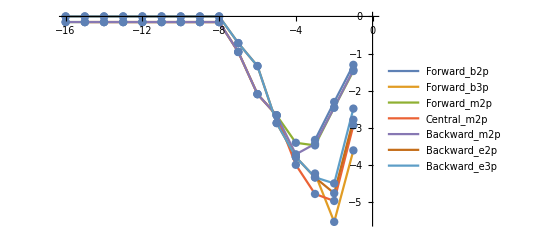

```mathematica
ListLinePlot[{row1, row2, row3, row4, row5,row6, row7},  Mesh->All, PlotLegends-> {"Forward_b2p", "Forward_b3p", "Forward_m2p", "Central_m2p", "Backward_m2p", "Backward_e2p", "Backward_e3p"}]
```

```mathematica
filedouble = "G:\\Studia\\IV\\MO\\Laboratoria\\8\\Program8\\Program8\\results_double.dat";
```

```mathematica
doubles = ReadList[filedouble, {Number, Number}];
```

```mathematica
d1 = Take[doubles, {1,6}];
d2=Take[doubles, {7,10}];
d3 = Take[doubles, {11,25}];
d4 = Take[doubles, {26,40}];
d5=Take[doubles, {41,55}];
d6 = Take[doubles, {56,70}];
d7 = Take[doubles, {71,85}];
```

```mathematica
dp1 = (Abs[Part[Part[d1,6], 2]-Part[Part[d1,1], 2]]) / (Abs[Part[Part[d1,6], 1] - Part[Part[d1,1], 1]])
```

1.00007

```mathematica
dp2 = (Abs[Part[Part[d2,4], 2]-Part[Part[d2,3], 2]]) / (Abs[Part[Part[d2,4], 1] - Part[Part[d2,3], 1]])
```

3.00005

```mathematica
dp3= (Abs[Part[Part[d3,15], 2]-Part[Part[d3,11], 2]]) / (Abs[Part[Part[d3,15], 1] - Part[Part[d3,11], 1]])
```

0.995985

```mathematica
dp4 = (Abs[Part[Part[d4,15], 2]-Part[Part[d4,14], 2]]) / (Abs[Part[Part[d4,15], 1] - Part[Part[d4,14], 1]])
```

2.04661

```mathematica
dp5 = (Abs[Part[Part[d5,15], 2]-Part[Part[d5,11], 2]]) / (Abs[Part[Part[d5,15], 1] - Part[Part[d5,11], 1]])
```

1.00414

```mathematica
dp6 = (Abs[Part[Part[d6,15], 2]-Part[Part[d6,12], 2]]) / (Abs[Part[Part[d6,15], 1] - Part[Part[d6,12], 1]])
```

2.07228

```mathematica
dp7 = (Abs[Part[Part[d7,15], 2]-Part[Part[d7,12], 2]]) / (Abs[Part[Part[d7,15], 1] - Part[Part[d7,12], 1]])
```

1.97402

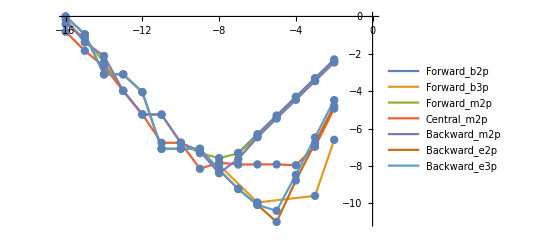

```mathematica
ListLinePlot[{d1, d2, d3, d4,d5, d6, d7},  Mesh->All, PlotLegends-> {"Forward_b2p", "Forward_b3p", "Forward_m2p", "Central_m2p", "Backward_m2p", "Backward_e2p", "Backward_e3p"}]
```